# AntennaLink

```mathematica
PacletDirectoryLoad["/Users/arnoudb/github/AntennaLink"];
```

```mathematica
Needs["ArnoudBuzing`AntennaLink`"]
```

```mathematica
(*Define a simple dipole antenna*)
wires={<|"Segments"->11,"Tag"->1,"P1"->{0,0,-0.25},"P2"->{0,0,0.25},"Radius"->0.001|>};

(*Set frequency (MHz)*)
freq=299.79;

(*Add excitation to the center segment (segment 6 of 11)*)
excitations={<|"Tag"->1,"Segment"->6,"Voltage"->1.0+0.0*I|>};

(*Run the solver directly in memory*)
results=AntennaSolveMemory[wires,freq,excitations];

(*Query the computed currents Dataset*)
results["Currents"]
```

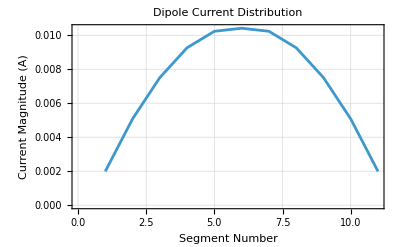

```mathematica
(*Calculate current magnitudes from Real and Imaginary parts*)
magnitudes=Normal[results["Currents"][All,Sqrt[#CurrentReal^2+#CurrentImag^2]&]];

(*Plot the 2D current distribution along the wire*)
ListLinePlot[magnitudes,PlotTheme->"Detailed",FrameLabel->{"Segment Number","Current Magnitude (A)"},PlotLabel->"Dipole Current Distribution"]
```

```mathematica
(*Quarter-wave monopole on Sommerfeld ground*)
monopole={<|"Segments"->5,"Tag"->1,"P1"->{0,0,0},"P2"->{0,0,0.25},"Radius"->0.001|>};
baseFeed={<|"Tag"->1,"Segment"->1,"Voltage"->1.0|>};

(*Solve over lossy earth using Sommerfeld method*)
solSommerfeld=AntennaSolveMemory[monopole,299.79,baseFeed,"Ground"-><|"Type"->"Sommerfeld","Dielectric"->15.0,"Conductivity"->0.01,"ConnectWires"->True|>];
```

```mathematica
(*5-element Yagi-Uda antenna*)
yagiWires=AntennaYagiUda[0.50,(*Reflector length*)
0.15,(*Reflector spacing*)
0.47,(*Driven element length*)
{0.44,0.43,0.42},(*Director lengths*)
{0.15,0.20,0.20},(*Spacings*)
0.002,(*Wire radius*)
11(*Segments per element*)]
```

{<|Segments→11,Tag→1,P1→{0.,-0.15,-0.25},P2→{0.,-0.15,0.25},Radius→0.002|>,<|Segments→11,Tag→2,P1→{0.,0.,-0.235},P2→{0.,0.,0.235},Radius→0.002|>,<|Segments→11,Tag→3,P1→{0.,0.15,-0.22},P2→{0.,0.15,0.22},Radius→0.002|>,<|Segments→11,Tag→4,P1→{0.,0.35,-0.215},P2→{0.,0.35,0.215},Radius→0.002|>,<|Segments→11,Tag→5,P1→{0.,0.55,-0.21},P2→{0.,0.55,0.21},Radius→0.002|>}

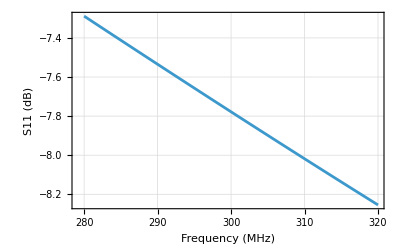

```mathematica
wires={<|"Segments"->11,"Tag"->1,"P1"->{0,0,-0.25},"P2"->{0,0,0.25},"Radius"->0.001|>};
excitations={<|"Tag"->1,"Segment"->6,"Voltage"->1.0|>};

(*Sweep from 280 to 320 MHz in steps of 2 MHz with a 50 ohm reference impedance*)
sweepResults=AntennaSweepMemory[wires,Range[280.0,320.0,2.0],excitations,"ReferenceImpedance"->50.0];

(*Plot return loss S11*)
ListLinePlot[Normal[sweepResults[All,{#Frequency,#S11}&]],PlotRange->All,FrameLabel->{"Frequency (MHz)","S11 (dB)"},PlotTheme->"Detailed"]
```

```mathematica
(*1-wavelength loop far field grid*)loop=AntennaHelix[0.16,0.0,1.0,0.001,24];
feed={<|"Tag"->1,"Segment"->1,"Voltage"->1.0|>};

(*Run theta and phi grid*)
ffData=AntennaFarFieldMemory[loop,300.0,feed,Range[0.0,180.0,5.0],(*Theta angles*)Range[0.0,360.0,10.0] (*Phi angles*)];
```

```mathematica
(*Extract {X,Y,Z} coordinates and corresponding Current Magnitude*)
data3D=Normal[results["Currents"][All,{#X,#Y,#Z}->#Magnitude&]]

(*Create a 3D plot where point color represents the current magnitude*)
ListPointPlot3D[data3D,ColorFunction->"Rainbow",PlotStyle->PointSize[0.05],AxesLabel->{"X","Y","Z"},BoxRatios->{1,1,3},PlotLabel->"3D Current Distribution"]
```

Failure[Dataset,{MessageTemplate:>Dataset::partmismatch,MessageParameters→<|Type→TypeSystem`Struct[{CurrentReal,CurrentImag,X,Y,Z},{TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real]}],Part→Magnitude,Symbol→Part|>}]

ListPointPlot3D::ldata: Failure[Dataset,{MessageTemplate:>Dataset::partmismatch,MessageParameters→<|Type→TypeSystem`Struct[{CurrentReal,CurrentImag,X,Y,Z},{TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real]}],Part→Magnitude,Symbol→Part|>}] is not a valid dataset or list of datasets.

ListPointPlot3D[Failure[Dataset,{MessageTemplate:>Dataset::partmismatch,MessageParameters→<|Type→TypeSystem`Struct[{CurrentReal,CurrentImag,X,Y,Z},{TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real]}],Part→Magnitude,Symbol→Part|>}],ColorFunction→Rainbow,PlotStyle→PointSize[0.05],AxesLabel→{X,Y,Z},BoxRatios→{1,1,3},PlotLabel→3D Current Distribution]

```mathematica
data3D
```

Failure[Dataset,{MessageTemplate:>Dataset::partmismatch,MessageParameters→<|Type→TypeSystem`Struct[{CurrentReal,CurrentImag,X,Y,Z},{TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real]}],Part→Magnitude,Symbol→Part|>}]

```mathematica
(*Extract {X,Y,Z} coordinates and compute Current Magnitude*)data3D=Normal[results["Currents"][All,{#X,#Y,#Z}->Sqrt[#CurrentReal^2+#CurrentImag^2]&]];

(*Create a 3D plot where point color represents the current magnitude*)
ListPointPlot3D[data3D,ColorFunction->"Rainbow",PlotStyle->PointSize[0.05],AxesLabel->{"X","Y","Z"},BoxRatios->{1,1,3},PlotLabel->"3D Current Distribution"]
```

-Graphics3D-

```mathematica
(*Define temporary file paths*)necFile=FileNameJoin[{$TemporaryDirectory,"dipole.nec"}];
outFile=FileNameJoin[{$TemporaryDirectory,"dipole.out"}];

(*Write a standard NEC-2 input file for a simple dipole*)
Export[necFile,"CM Simple Dipole
CE
GW 1 11 0 0 -0.25 0 0 0.25 0.001
GE 0
EX 0 1 6 0 1.0 0.0
FR 0 1 0 0 299.79 0
XQ
EN
","String"];

(*Run the solver*)
AntennaSolve[necFile,outFile]
```

/private/var/folders/2h/44nt1g317xz3vyzht44m7060000_nk/T/dipole.out

```mathematica
necFile=FileNameJoin[{$TemporaryDirectory,"dipole.nec"}];
outFile=FileNameJoin[{$TemporaryDirectory,"dipole.out"}];

Export[necFile,"CM Simple Dipole
CE
GW 1 11 0 0 -0.25 0 0 0.25 0.001
GE 0
EX 0 1 6 0 1.0 0.0
FR 0 1 0 0 299.79 0
RP 0 37 73 1000 -90.0 0.0 5.0 5.0 100000.0
XQ
EN
","String"];

AntennaSolve[necFile,outFile]
```

/private/var/folders/2h/44nt1g317xz3vyzht44m7060000_nk/T/dipole.out

```mathematica
(*Parse results from a simulation that included an RP card*)results=AntennaParseOutput[outFile];
rp=results["RadiationPattern"];

(*Filter out placeholder values (NEC uses-999.99 for undefined gains)*)
(*And shift the gain to be positive for the radius (e.g.,if max gain is 2.17,add offset)*)
minGain=Min[Normal[rp[All,#TotalGain&]]];
offset=Abs[minGain]+1;

(*Convert Spherical (Theta,Phi) and Gain (Radius) to Cartesian {X,Y,Z}*)
(*Note:NEC-2 Theta is often elevation from the XY plane depending on RP card config*)
points3D=Normal[rp[All,With[{r=#TotalGain+offset,th=#Theta*Degree,ph=#Phi*Degree},{r*Cos[th]*Cos[ph],r*Cos[th]*Sin[ph],r*Sin[th]}]&]];

(*Create a 3D Point Plot colored by Z-height (or Gain)*)
ListPointPlot3D[points3D,ColorFunction->"Rainbow",PlotStyle->PointSize[0.02],BoxRatios->{1,1,1},AxesLabel->{"X","Y","Z"},PlotLabel->"3D Radiation Pattern"]
```

-Graphics3D-

```mathematica
points3D
```

```mathematica
ListContourPlot3D[points3D,ColorFunction->"Rainbow",BoxRatios->{1,1,1},AxesLabel->{"X","Y","Z"},PlotLabel->"3D Radiation Pattern",Mesh->None]
```

-Graphics3D-

```mathematica
(*Define the elements of the Yagi-Uda Antenna*)wires={(*1. Reflector (Longer than dipole,placed behind it)*)<|"Segments"->11,"Tag"->1,"P1"->{-0.25,0,-0.2625},"P2"->{-0.25,0,0.2625},"Radius"->0.001|>,(*2. Driven Element (The actual dipole)*)<|"Segments"->11,"Tag"->2,"P1"->{0,0,-0.2375},"P2"->{0,0,0.2375},"Radius"->0.001|>,(*3. Director (Shorter than dipole,placed in front of it)*)<|"Segments"->11,"Tag"->3,"P1"->{0.25,0,-0.225},"P2"->{0.25,0,0.225},"Radius"->0.001|>};

(*Frequency in MHz*)
freq=299.79;

(*Excitation is ONLY applied to the center (Segment 6) of the Driven Element (Tag 2)*)
excitations={<|"Tag"->2,"Segment"->6,"Voltage"->1.0+0.0 I|>};

(*Solve in memory!*)
results=AntennaSolveMemory[wires,freq,excitations];

(*Look at the structured currents across all 3 elements*)
results["Currents"]
```

```mathematica
results["Curr"]
```

```mathematica
(*1. Load the paclet*)PacletDirectoryLoad["/Users/arnoudb/github/AntennaLink/AntennaLink"];
Needs["ArnoudBuzing`AntennaLink`"];

(*2. Define Temporary Files*)
necFile=FileNameJoin[{$TemporaryDirectory,"yagi.nec"}];
outFile=FileNameJoin[{$TemporaryDirectory,"yagi.out"}];

(*3. Write the NEC-2 Configuration for a 3-Element Yagi-Uda*)
(*It includes the Reflector (GW 1),Driven Element (GW 2),and Director (GW 3)*)
(*As well as the RP (Radiation Pattern) card!*)
Export[necFile,"CM 3-Element Yagi-Uda Antenna
CE
GW 1 11 -0.25 0.0 -0.2625 -0.25 0.0 0.2625 0.001
GW 2 11 0.0 0.0 -0.2375 0.0 0.0 0.2375 0.001
GW 3 11 0.25 0.0 -0.225 0.25 0.0 0.225 0.001
GE 0
EX 0 2 6 0 1.0 0.0
FR 0 1 0 0 299.79 0
RP 0 37 73 1000 -90.0 0.0 5.0 5.0 100000.0
XQ
EN
","String"];

(*4. Run the Solver*)
AntennaSolve[necFile,outFile];

(*5. Parse the Outputs*)
results=AntennaParseOutput[outFile];
rp=results["RadiationPattern"];

(*6. Process the 3D Radiation Pattern Data*)
(*Filter out placeholder values (NEC uses-999.99 for undefined gains)*)
minGain=Min[Normal[rp[All,#TotalGain&]]];
offset=Abs[minGain]+1;

(*Map Spherical (Theta,Phi) and Gain to Cartesian (X,Y,Z) space*)
points3D=Normal[rp[All,With[{r=#TotalGain+offset,th=#Theta*Degree,ph=#Phi*Degree},{r*Cos[th]*Cos[ph],r*Cos[th]*Sin[ph],r*Sin[th]}]&]];

(*7. Render the stunning 3D Directional Lobe!*)
ListPointPlot3D[points3D,ColorFunction->"Rainbow",PlotStyle->PointSize[0.02],BoxRatios->{1,1,1},AxesLabel->{"X","Y","Z"},PlotLabel->"3D Yagi-Uda Radiation Pattern"]
```

-Graphics3D-

```mathematica
(*1. Filter out the-999.99 placeholder values*)validRP=Select[Normal[rp],#TotalGain>-900&];

(*2. Calculate a 40dB dynamic range to create deep,visible nulls*)
maxGain=Max[validRP[[All,"TotalGain"]]];
dynamicRange=40;
minGainDisplay=maxGain-dynamicRange;

(*3. Map to Colatitude (0 to Pi) and Azimuth (0 to 2Pi) for SphericalPlot3D*)
(*We use Max[0,Gain-minGainDisplay] so the weakest signals pull all the way to the origin*)
gainPoints={{Pi/2-(#Theta*Degree),#Phi*Degree},Max[0,#TotalGain-minGainDisplay]}&/@validRP;

(*4. Create an interpolation function over the spherical grid*)
gainFunc=Interpolation[gainPoints,InterpolationOrder->1];

(*5. Render a solid,colorful 3D lobe!*)
SphericalPlot3D[gainFunc[colat,az],{colat,0,Pi},{az,0,2 Pi},ColorFunction->"Rainbow",Mesh->None,(*Remove the wireframe lines for a smooth look*)PlotPoints->60,(*Increase resolution for smooth curves*)Boxed->False,Axes->False,PlotLabel->"3D Yagi-Uda Radiation Pattern"]
```

-Graphics3D-

```mathematica
(*Helix aligned along the Z-axis*)
helixWires=AntennaHelix[0.08,(*Coil radius*)0.10,(*Turn pitch*)5.0,(*Number of turns*)0.001,(*Wire radius*)16     (*Segments per turn*)];
```

```mathematica
(*Solve helical antenna*)
sol=AntennaSolveMemory[helixWires,300.0,{<|"Tag"->1,"Segment"->1,"Voltage"->1.0|>}];
```

```mathematica
(*Render colored by current magnitude with excitation bases highlighted*)
AntennaPlotGeometry[sol]
```

-Graphics3D-

```mathematica
(*Render colored by current phase*)
AntennaPlotGeometry[sol,"ColorFunction"->"Phase"]
```

-Graphics3D-